```mathematica
Кома
```

```mathematica
l[R_,h_,d_,α_,n_]:=√((R-h)^2+d^2);
β[R_,h_,d_,α_,n_]:=ArcSin[Sin[α]/n];
ξ[R_,h_,d_,α_,n_]:=ArcTan[d/(R-h)];
Subscript[γ, 1][R_,h_,d_,α_,n_]:=ArcSin[(l[R,h,d,α,n]*Sin[ξ[R,h,d,α,n]-β[R,h,d,α,n]])/R];
Subscript[γ, 2][R_,h_,d_,α_,n_]:=ArcSin[(l[R,h,d,α,n]*Sin[ξ[R,h,d,α,n]+β[R,h,d,α,n]])/R];
Subscript[η, 1][R_,h_,d_,α_,n_]:=Subscript[γ, 1][R,h,d,α,n]+β[R,h,d,α,n];
Subscript[η, 2][R_,h_,d_,α_,n_]:=Subscript[γ, 2][R,h,d,α,n]-β[R,h,d,α,n];
Subscript[y, 1][R_,h_,d_,α_,n_]:=R*Sin[Subscript[η, 1][R,h,d,α,n]];
Subscript[y, 2][R_,h_,d_,α_,n_]:=-R*Sin[Subscript[η, 2][R,h,d,α,n]];
Subscript[x, 1][R_,h_,d_,α_,n_]:=R*Cos[Subscript[η, 1][R,h,d,α,n]];
Subscript[x, 2][R_,h_,d_,α_,n_]:=R*Cos[Subscript[η, 2][R,h,d,α,n]];
Subscript[δ, 1][R_,h_,d_,α_,n_]:=ArcSin[n*Sin[Subscript[γ, 1][R,h,d,α,n]]];
Subscript[δ, 2][R_,h_,d_,α_,n_]:=ArcSin[n*Sin[Subscript[γ, 2][R,h,d,α,n]]];
Subscript[ω, 1][R_,h_,d_,α_,n_]:=Subscript[δ, 1][R,h,d,α,n]-Subscript[η, 1][R,h,d,α,n];
Subscript[ω, 2][R_,h_,d_,α_,n_]:=Subscript[δ, 2][R,h,d,α,n]-Subscript[η, 2][R,h,d,α,n];
x[R_,h_,d_,α_,n_]:=(Subscript[y, 1][R,h,d,α,n]-Subscript[y, 2][R,h,d,α,n]+Subscript[x, 1][R,h,d,α,n]*Tan[Subscript[ω, 1][R,h,d,α,n]]+Subscript[x, 2][R,h,d,α,n]*Tan[Subscript[ω, 2][R,h,d,α,n]]) /(Tan[Subscript[ω, 1][R,h,d,α,n]]+Tan[Subscript[ω, 2][R,h,d,α,n]]);
y[R_,h_,d_,α_,n_]:=Subscript[y, 1][R,h,d,α,n]-(x[R,h,d,α,n]-Subscript[x, 1][R,h,d,α,n])*Tan[Subscript[ω, 1][R,h,d,α,n]];
```

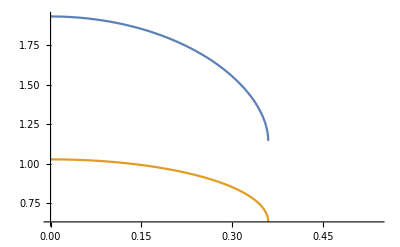

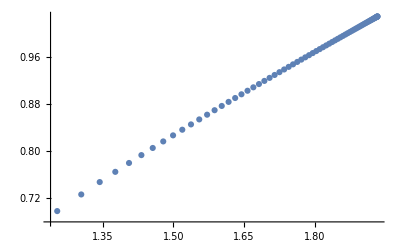

```mathematica
rr=1;
hh=0.3;
aa=50*Degree;
nn=1.5;
Plot[{Subscript[γ, 1][rr,hh,d,aa,nn]/Degree,Subscript[γ, 2][rr,hh,d,aa,nn]/Degree, 41.81},{d,0,0.54}];
Plot[{Subscript[ω, 1][rr,hh,d,aa,nn]/Degree,Subscript[ω, 2][rr,hh,d,aa,nn]/Degree},{d,0,0.54}];
Plot[{x[rr,hh,d,aa,nn],y[rr,hh,d,aa,nn]},{d,0,0.54}]
data[i_, R_,h_,a_,n_]:=Table[{x[R,h,d,a,n],y[R,h,d,a,n]},{d,0.000001,i,0.005}];
ListPlot[data[0.54,rr,hh,aa,nn]]
```

```mathematica
dataExport[i_, R_,h_,a_,n_]:=SetPrecision[Table[{d, x[R,h,d,a,n],y[R,h,d,a,n]},{d,0.000001,i,0.005}],5]
dataExp=Join[{{"d","x","y"}},dataExport[0.360,rr,hh,aa,nn]];
file=Export[FileNameJoin[{NotebookDirectory[],"..","data","coma.txt"}], 
dataExp, "Table"];
```

```mathematica
Дисторсия
```

```mathematica
β0[R_,h_,d_,α_,n_]:=ArcSin[Sin[α]/n];
γ0[R_,h_,d_,α_,n_]:=ArcSin[((R-h)*Sin[β0[R,h,d,α,n]])/R];
η0[R_,h_,d_,α_,n_]:=β0[R,h,d,α,n]-γ0[R,h,d,α,n];
δ0[R_,h_,d_,α_,n_]:=ArcSin[n*Sin[γ0[R,h,d,α,n]]];
y0[R_,h_,d_,α_,n_]:=R*Sin[η0[R,h,d,α,n]];
x0[R_,h_,d_,α_,n_]:=R*Cos[η0[R,h,d,α,n]];
ω0[R_,h_,d_,α_,n_]:=η0[R,h,d,α,n]+δ0[R,h,d,α,n];
y00[R_,h_,d_,α_,n_]:=y0[R,h,d,α,n]+(3R-x0[R,h,d,α,n])*Tan[ω0[R,h,d,α,n]];
```

```mathematica
hhh=0.1;
dataDistortion[R_,h_,d_,n_]:=
Table[{SetPrecision[a/Degree,5], SetPrecision[y00[R,h,d,a,n],5],SetPrecision[2*Tan[a],5]},{a,0*Degree,89*Degree,1*Degree}];
Plot[{y00[1,hhh,0.0001,a,1.5], 2*Tan[a]},{a,0*Degree,90*Degree}]
dataExp=Join[{{"alpha","y","tan"}},dataDistortion[1,hhh,0.00001,1.5]];
file=Export[FileNameJoin[{NotebookDirectory[],"..","data","distorsion-y.txt"}], 
dataExp, "Table"];
FilePrint[file];
```

```mathematica
dataExp=SetPrecision[Join[{{"x","y"}},Table[{x[1,0.3,0.001,a,1.5],y[1,0.3,0.001,a,1.5]},{a,0,90*Degree,1*Degree}]],5];
file=Export[FileNameJoin[{NotebookDirectory[],"..","data","distorsion-xy.txt"}], 
dataExp, "Table"];
```